```mathematica
dataC=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/324/T.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]]
```

{{C, mkF,x_0,n,x,T, мс, Sigma Te,T теор,Sigma Tt},{0.02,6.,2.,0.7,0.58,0.2,0.56,0.01},{0.09,3.,2.,0.6,1.,0.39,1.18,0.02},{0.15,6.,4.,3.5,1.46,0.17,1.52,0.02},{0.22,6.,3.,3.,1.67,0.21,1.84,0.02},{0.35,6.,3.,3.3,1.83,0.22,2.32,0.03},{0.48,6.,3.,4.,2.22,0.26,2.72,0.04},{0.59,6.5,3.,4.5,2.31,0.26,3.02,0.04},{0.75,6.5,2.,3.4,2.62,0.32,3.4,0.04},{0.87,6.5,2.,4.3,3.31,0.38,3.66,0.05},{0.9,6.5,2.,4.6,3.54,0.4,3.72,0.05}}

```mathematica
dataC//TableForm
```

C, mkF | x_0 | n | x | T, мс |  Sigma Te | T теор | Sigma Tt
0.02 | 6. | 2. | 0.7 | 0.58 | 0.2 | 0.56 | 0.01
0.09 | 3. | 2. | 0.6 | 1. | 0.39 | 1.18 | 0.02
0.15 | 6. | 4. | 3.5 | 1.46 | 0.17 | 1.52 | 0.02
0.22 | 6. | 3. | 3. | 1.67 | 0.21 | 1.84 | 0.02
0.35 | 6. | 3. | 3.3 | 1.83 | 0.22 | 2.32 | 0.03
0.48 | 6. | 3. | 4. | 2.22 | 0.26 | 2.72 | 0.04
0.59 | 6.5 | 3. | 4.5 | 2.31 | 0.26 | 3.02 | 0.04
0.75 | 6.5 | 2. | 3.4 | 2.62 | 0.32 | 3.4 | 0.04
0.87 | 6.5 | 2. | 4.3 | 3.31 | 0.38 | 3.66 | 0.05
0.9 | 6.5 | 2. | 4.6 | 3.54 | 0.4 | 3.72 | 0.05

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
```

```mathematica
Needs@"ErrorBarPlots`";
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
myTicks[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
forFit=(*Select[*)dataC⟦2;;,{7,5}⟧(*,First@#>22&]*);
fit=LinearModelFit[forFit(*⟦All,;;2⟧*),{x,1},x];
forFit
fit@"ParameterTable"
fit@"Function"
```

{{0.56,0.58},{1.18,1.},{1.52,1.46},{1.84,1.67},{2.32,1.83},{2.72,2.22},{3.02,2.31},{3.4,2.62},{3.66,3.31},{3.72,3.54}}

| Estimate | Standard Error | t-Statistic | P-Value
x | 0.841518 | 0.0677413 | 12.4225 | 1.64621×10^-6
1 | 0.0394052 | 0.176774 | 0.222913 | 0.829189

0.0394052+0.841518 #1&

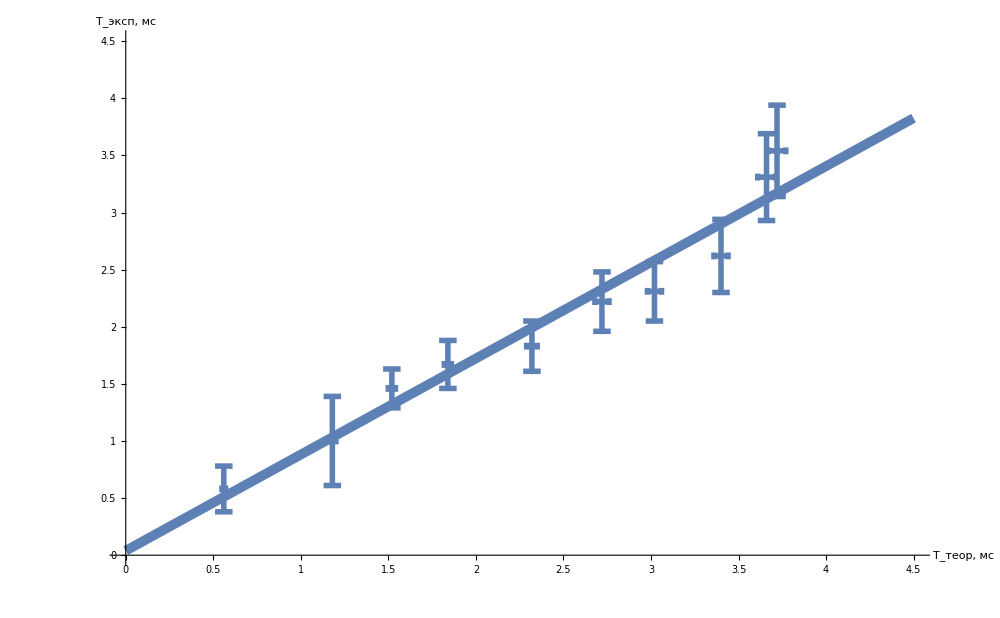

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataC⟦2;;,{7,5,8,6}⟧,
GridLines->{grids@0.5,grids@0.2},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"T_(:0442:0435:043e:0440), мс","T_(:044d:043a:0441:043f), мс"},
AxesStyle->Directive[Large,Black],
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)}],
PlotMarkers->{Automatic,0.01},Joined->False,PlotStyle->Thickness@0.1,
PlotRange->{{0.0,4.5},{0.0000000,4.5}},Ticks->myTicks,
ImageSize->1000],Plot[fit["Function"]@x,{x,0,4.5}, PlotStyle->Thickness@0.007]]
```

```mathematica
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
forTeXC=MapAt[dropLastDot@*ToString,dataC,{{2;;,All}}];
forTeXC//TeXForm
```

\left(
\begin{array}{cccccccc}
 \text{C, mkF} & \text{x$\_$0} & \text{n} & \text{x} & \text{T, $\unicode{043c}\unicode{0441}$} & \text{Sigma Te} & \text{T
   $\unicode{0442}\unicode{0435}\unicode{043e}\unicode{0440}$} & \text{Sigma Tt} \\
 0.02 & 6 & 2 & 0.7 & 0.58 & 0.2 & 0.56 & 0.01 \\
 0.09 & 3 & 2 & 0.6 & 1 & 0.39 & 1.18 & 0.02 \\
 0.15 & 6 & 4 & 3.5 & 1.46 & 0.17 & 1.52 & 0.02 \\
 0.22 & 6 & 3 & 3 & 1.67 & 0.21 & 1.84 & 0.02 \\
 0.35 & 6 & 3 & 3.3 & 1.83 & 0.22 & 2.32 & 0.03 \\
 0.48 & 6 & 3 & 4 & 2.22 & 0.26 & 2.72 & 0.04 \\
 0.59 & 6.5 & 3 & 4.5 & 2.31 & 0.26 & 3.02 & 0.04 \\
 0.75 & 6.5 & 2 & 3.4 & 2.62 & 0.32 & 3.4 & 0.04 \\
 0.87 & 6.5 & 2 & 4.3 & 3.31 & 0.38 & 3.66 & 0.05 \\
 0.9 & 6.5 & 2 & 4.6 & 3.54 & 0.4 & 3.72 & 0.05 \\
\end{array}
\right)

```mathematica
dataR=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/324/R.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]]
```

{{R,n,U_k,U_k+n,\theta,Sigma \,Rк,Sigma R},{1100.,3.,3.,0.9,0.4,0.05,1142.,2.},{1400.,3.,3.,0.6,0.54,0.09,1442.,3.},{1800.,2.,2.9,0.8,0.64,0.08,1842.,4.},{2200.,2.,2.8,0.6,0.77,0.13,2242.,4.},{2500.,1.,2.7,1.,0.99,0.11,2542.,5.},{2700.,1.,2.6,0.9,1.06,0.12,2742.,5.},{3300.,1.,2.5,0.8,1.14,0.15,3342.,7.},{3600.,1.,2.5,0.7,1.27,0.19,3642.,7.}}

```mathematica
dataR//TableForm
```

R | n | U_k | U_k+n | \theta | Sigma \ | Rк | Sigma R
1100. | 3. | 3. | 0.9 | 0.4 | 0.05 | 1142. | 2.
1400. | 3. | 3. | 0.6 | 0.54 | 0.09 | 1442. | 3.
1800. | 2. | 2.9 | 0.8 | 0.64 | 0.08 | 1842. | 4.
2200. | 2. | 2.8 | 0.6 | 0.77 | 0.13 | 2242. | 4.
2500. | 1. | 2.7 | 1. | 0.99 | 0.11 | 2542. | 5.
2700. | 1. | 2.6 | 0.9 | 1.06 | 0.12 | 2742. | 5.
3300. | 1. | 2.5 | 0.8 | 1.14 | 0.15 | 3342. | 7.
3600. | 1. | 2.5 | 0.7 | 1.27 | 0.19 | 3642. | 7.

```mathematica
forTeXR=MapAt[dropLastDot@*ToString,dataR,{{2;;,All}}];
forTeXR//TeXForm
```

\left(
\begin{array}{cccccccc}
 \text{R} & \text{n} & \text{U$\_$k} & \text{U$\_$k+n} & \text{$\backslash \backslash $theta} & \text{Sigma $\backslash \texttt{"}$} &
   \text{R$\unicode{043a}$} & \text{Sigma R} \\
 1100 & 3 & 3 & 0.9 & 0.4 & 0.05 & 1142 & 2 \\
 1400 & 3 & 3 & 0.6 & 0.54 & 0.09 & 1442 & 3 \\
 1800 & 2 & 2.9 & 0.8 & 0.64 & 0.08 & 1842 & 4 \\
 2200 & 2 & 2.8 & 0.6 & 0.77 & 0.13 & 2242 & 4 \\
 2500 & 1 & 2.7 & 1 & 0.99 & 0.11 & 2542 & 5 \\
 2700 & 1 & 2.6 & 0.9 & 1.06 & 0.12 & 2742 & 5 \\
 3300 & 1 & 2.5 & 0.8 & 1.14 & 0.15 & 3342 & 7 \\
 3600 & 1 & 2.5 & 0.7 & 1.27 & 0.19 & 3642 & 7 \\
\end{array}
\right)

```mathematica
forTeXGr=MapAt[dropLastDot@*ToString,dataGr,{{2;;,All}}];
forTeXGr//TeXForm
```

\left(
\begin{array}{ccc}
 \text{1/$\backslash \backslash $th} & \text{sig} & \text{1/R${}^{\wedge}$2 10-6} \\
 6.21 & 0.75 & 0.77 \\
 3.47 & 0.68 & 0.48 \\
 2.41 & 0.63 & 0.29 \\
 1.69 & 0.57 & 0.2 \\
 1.01 & 0.22 & 0.15 \\
 0.89 & 0.21 & 0.13 \\
 0.77 & 0.2 & 0.09 \\
 0.62 & 0.18 & 0.08 \\
\end{array}
\right)

```mathematica
dataGr=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/324/teta.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]]
dataGr//TableForm
```

{{1/\th,sig,1/R^2 10-6},{6.21,0.75,0.77},{3.47,0.68,0.48},{2.41,0.63,0.29},{1.69,0.57,0.2},{1.01,0.22,0.15},{0.89,0.21,0.13},{0.77,0.2,0.09},{0.62,0.18,0.08}}

1/\th | sig | 1/R^2 10-6
6.21 | 0.75 | 0.77
3.47 | 0.68 | 0.48
2.41 | 0.63 | 0.29
1.69 | 0.57 | 0.2
1.01 | 0.22 | 0.15
0.89 | 0.21 | 0.13
0.77 | 0.2 | 0.09
0.62 | 0.18 | 0.08

```mathematica
forFit=(*Select[*)dataGr⟦2;;,{3,1}⟧(*,First@#>22&]*);
fit=LinearModelFit[forFit(*⟦All,;;2⟧*),{x,1},x];
forFit
fit@"ParameterTable"
fit@"Function"
```

{{0.77,6.21},{0.48,3.47},{0.29,2.41},{0.2,1.69},{0.15,1.01},{0.13,0.89},{0.09,0.77},{0.08,0.62}}

```mathematica
{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {x, 7.957906853747322, 0.28153265746757256, 28.26637209810705, 1.2976379087486643*^-7}, {1, -0.044727001213329225, 0.09960150353354393, -0.4490594983665684, 0.6691529353975434}}
```

| Estimate | Standard Error | t-Statistic | P-Value
x | 7.95791 | 0.281533 | 28.2664 | 1.29764×10^-7
1 | -0.044727 | 0.0996015 | -0.449059 | 0.669153

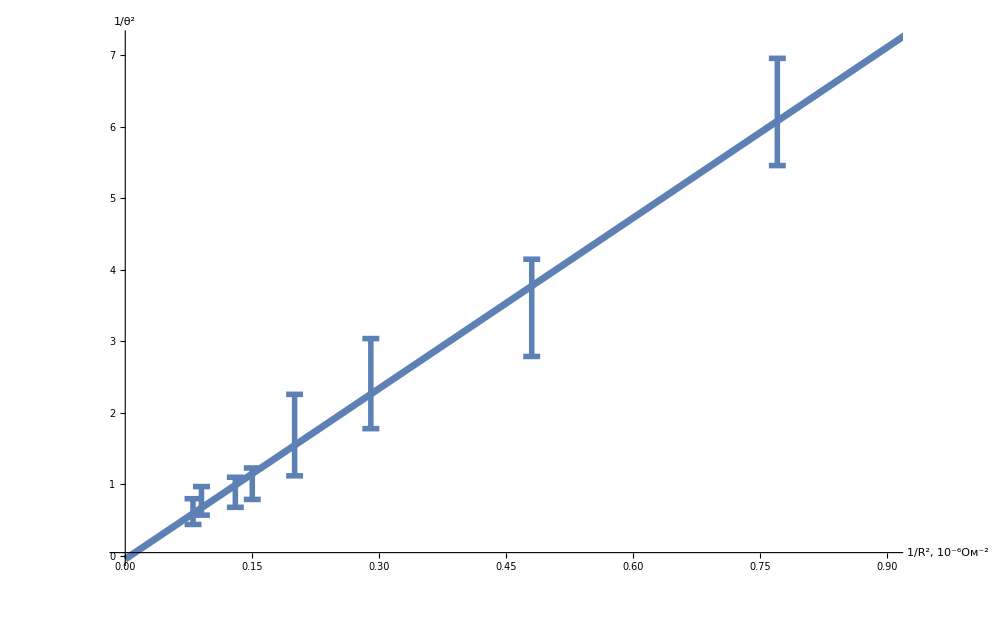

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataGr⟦2;;,{3,1,3,2}⟧,
GridLines->{grids@0.05,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"1/R^2, 10^-6(:041e:043c)^-2","1/θ^2"},
AxesStyle->Directive[Large,Black],
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),(*horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)}],
PlotMarkers->{Automatic,0.01},Joined->False,PlotStyle->Thickness@0.1,
PlotRange->{{-0.000001, 0.9},{0.01,7.2}},(*Ticks->myTicks,*)
ImageSize->1000],Plot[fit["Function"]@x,{x,0,4.5}, PlotStyle->Thickness@0.005]]
```